# Physics through Computational Thinking Lecture-3

## Visual Thinking-3

Auditya Sharma and Ambar Jain

Dept. of Physics, IISER Bhopal

Outline

In this lecture you will

1. learn to plot various functions and identify their salient properties

2. learn to plot 2-D and 3-D plots such as vector plots, streamline plots and contour plots.

10-Jan-2019

### Properties of Functions: Zeros, divergences, extrema and asymptotes

### Zero

Zero: A function f(x) has zeros at points x^* where f(x^*)=0. Identifying these points should be the first step in sketching a function.

f(x)=x^2-3x+2
= (x-2)(x-1).

Factorization (when possible) helps immediately identify the zeros.

```mathematica
Plot[x^2-3x+2,{x,0,3}];
```

### Divergence

Divergence: A function f(x) has divergences (or singularities) at points x^* where 1/(f(x^*))has a zero. Identifying these points (and sometimes the form of the divergence nearby) helps us figure out where and how the function blows up.

f(x)= 1/((x-2)(x-1)).

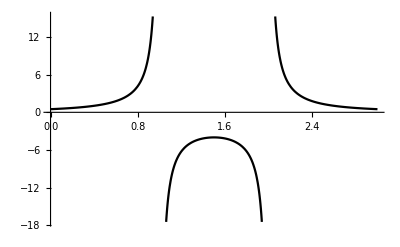

```mathematica
Plot[1/((x-1)(x-2)),{x,0,3}]
```

### Extrema

Extrema: A function f(x) has extrema at points x^* where f'(x^*)=0. Further work would be essential to clarify if the point is a minimum or a maximum or an inflection point. Identifying these points help in getting the broad shape of the function. Let us take the example of the same function f(x)=x^2-3x+2. Here it turns out that rather than factorization, it is more useful to `complete the squares’.

f(x)=x^2-3x+2
= (x-3/2)^2-1/4.

```mathematica
Plot[x^2-3x+2,{x,0.5,2.5},PlotRange->{-0.3,0.3}];
```

### Asymptote

Asymptote: An asymptote is a curve that a function f(x) approaches arbitrarily closely in some limit. A familiar example is the curve f(x)= 1/x, which asymptotically approaches the X-axis as x→∞, and asymptotically approaches the Y-axis as x→0.

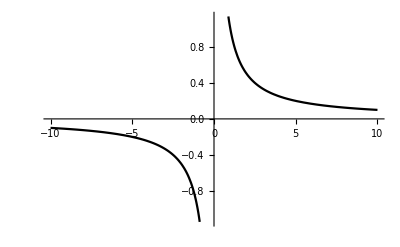

```mathematica
Plot[1/x,{x,-10,10}]
```

Let’s increase the y-range of the plot and examine it whether the curve 1/x approaches y-axis. We will do this by invoking an option for the Plot function called PlotRange

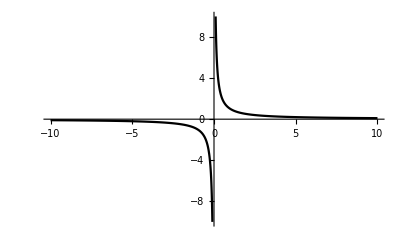

```mathematica
Plot[1/x,{x,-10,10},PlotRange->{-10,10}]
```

### Properties of Functions

### Example-1

For the function f(x) shown below find the extremum points if any and find the nature of the extremum:

f(x)=x |x|

```mathematica
Plot[{x Abs[x]}, {x, -4, 4}]
```

### Example-2

For the function f(x) shown below find the behaviour of the function in various regions and identify domains of continuity and differentiability.

f(x)=(|x|)^(1/3)

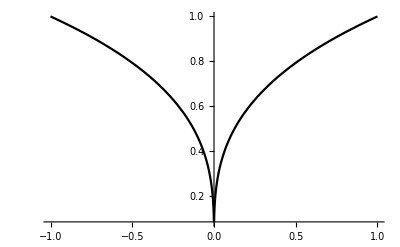

```mathematica
Plot[{Abs[x]^(1/3)},{x,-1,1}]
```

### Example-3

For the famous function known as Lorentzian shown below, plot the function and identify what happens by changing the parameter a. What is the asymptotic behaviour of the function?

f_Lorentzian(x)=a^2/(x^2+a^2)

```mathematica
Manipulate[Plot[{a^2/(x^2+a^2)},{x,-5,5},PlotRange->{0,1},PlotLegends->{"Lorentzian","a^2/x^2"}],{a,0.5,2,0.1}]
```

### Example-4

Let’s change the sign of a^2 in the Lorentzian to get the not-so-famous function shown below. Can you plot this and identify the divergences?

f(x)=1/(x^2-a^2)

Do this on paper and pen before we test it out on the computer. Discuss in groups of three.

```mathematica
Manipulate[Plot[1/(x^2-a^2),{x,-5,5},PlotRange->Full,PlotLabel->Style["a"->a,16,Blue]],{a,0.5,2,0.1}]
```

### Example-5

For the function below, find the asymptotes.

f(x)=((x-1)(x-2))/x

Do this on paper and pen before we test it out on the computer. Discuss in groups of three.

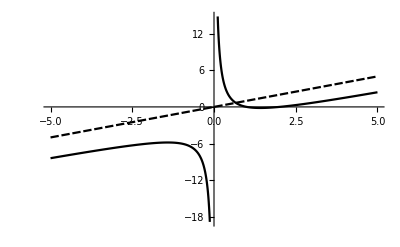

```mathematica
Plot[{(x - 1) (x - 2)/x,x}, {x, -5, 5}]
```

### Example-6

Here is another famous function: Gaussian

f_Gaussian(x)=ⅇ^(-x^2/a^2)

Study the properties of this function and explore the role of parameter a.

```mathematica
Manipulate[Plot[{Exp[-x^2/a^2],Exp[-1]},{x,-5,5},PlotRange->Full,PlotLabel->Style["a"->a,16,Blue],PlotLegends->{"Gaussian",ⅇ^-1,"Lorentzian"}],{a,0.5,2,0.1}]
```

### Hyperbolic Trigonometric Functions

Definitions of Hyperbolic Trigonometric functions

function | definition | WL usage | Notes
sinh(x) | 1/2 (ⅇ^x-ⅇ^-x) | Sinh[x] |  
cosh(x) | 1/2 (ⅇ^-x+ⅇ^x) | Cosh[x] |  
tanh(x) | (ⅇ^x-ⅇ^-x)/(ⅇ^-x+ⅇ^x) | Tanh[x] |  
cosech(x) | 2/(ⅇ^x-ⅇ^-x) | Csch[x] | 1/(sinh(x))
sech(x) | 2/(ⅇ^-x+ⅇ^x) | Sech[x] | 1/(cosh(x))
coth(x) | (ⅇ^-x+ⅇ^x)/(ⅇ^x-ⅇ^-x) | Coth[x] | 1/(tanh(x))

### Problem

(a) For sinh(x), sech(x), tanh(x) and coth(x), make the plots in suitable ranges for the function. Identify the salient features, such as extrema, zeros, asymptotes, discontinuities, derivative discontinuities.

(b) Using the Manipulate command explore the effects of parameter a in functions sinh(a x), sech(a x), tanh(a x) and coth(a x)

(c) Compare the functions 1/(x^2+1), ⅇ^(-x^2) and sech(x) on the same plot. What is the difference between them for large x?

### Vector Fields

A vector field in 3-dimensions is a function represented by a 3-tuple of functions

v⃗(x,y,z)=(v_x(x,y,z), v_y(x,y,z), v_z(x,y,x))

It can also be represented as (where r⃗ is the position coordinate)

v⃗(r⃗)=(v_x(r⃗), v_y(r⃗), v_z(r⃗))

or in the unit vector notation:

v⃗(r⃗)=v_x(r⃗)î+ v_y(r⃗)ĵ+v_z(r⃗)k̂

In two dimensions (r⃗=x î+y ĵ)

v⃗(r⃗)=v_x(r⃗)î+ v_y(r⃗)ĵ

It is straightforward to generalize it to n-dimensions but it will be difficult to think about plots in n-dimensions \[FreakedSmiley]. So for now let’s focus on 2 and 3-dimensions.

### Example-1

(a) For the vector fields given below find their divergence and curl:

v⃗=x î+y ĵ
u⃗=y î+x ĵ
w⃗=-y î+x ĵ

(b) By creating a vector plot verify the results you found for divergence and curl of these functions.

(c) If these vector fields represented flow of a fluid, make a streamline plot to demonstrate it:

Sol (a):

OverVector[∇]·v⃗=2
OverVector[∇]×v⃗=0
OverVector[∇]·u⃗=0
OverVector[∇]×u⃗=0
OverVector[∇]·w⃗=0
OverVector[∇]×w⃗=2 k̂

Sol (b): In Mathematica, we will do this by invoking VectorPlot, where a vector field is represented by a 2-tuple or 3-tuple as given below:

v⃗={x,y}
u⃗={y,x}
w⃗={-y,x}

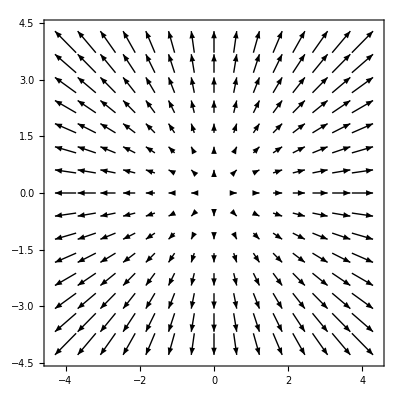

```mathematica
VectorPlot[{x,y},{x, -4, 4},{y,-4,4}]
```

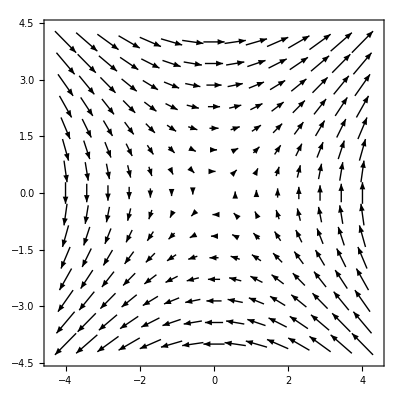

```mathematica
VectorPlot[{y,x},{x, -4, 4},{y,-4,4}]
```

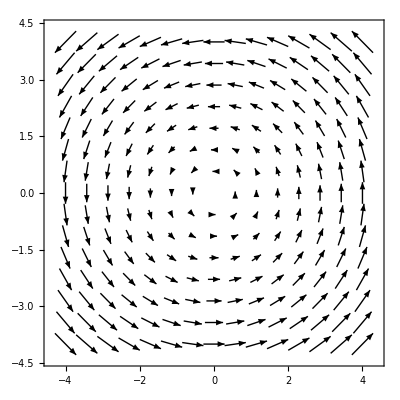

```mathematica
VectorPlot[{-y,x},{x, -4, 4},{y,-4,4}]
```

Sol (c): Streamline Plots are very similar to vector plots but they represent flow of a fluid or field lines, as in electric field lines and magnetic field lines. It only shows the direction of the flow at each point. They can be made by  StreamPlot function:

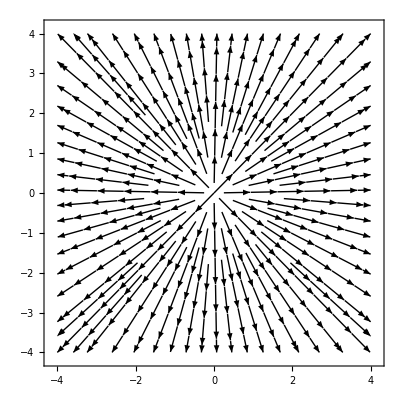

```mathematica
StreamPlot[{x,y},{x, -4, 4},{y,-4,4}]
```

To avoid the funny business at origin where the flow direction is “confusing”, we can avoid the region by using the option known as RegionFunction, which puts a suitable constraint on the coordinates x and y, vector field components v_x, v_y and norm of the vector field n=||v⃗||. In this case we subject the plot to constraint that x^2+y^2>0.05:

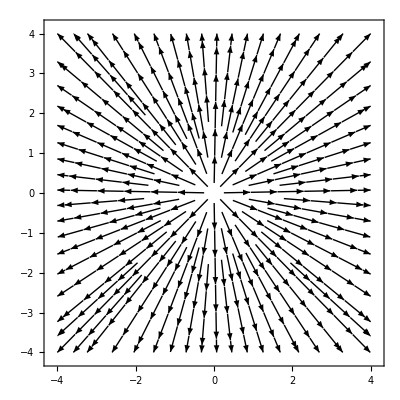

```mathematica
StreamPlot[{x,y},{x, -4, 4},{y,-4,4},RegionFunction->Function[{x,y,vx,vy,n},x^2+y^2>0.05]]
```

Using StreamDensityPlot, you can also get the idea about the norm of the vector field as well. Lighter the background implies bigger is the vector field. StreamDensityPlot is an alternate to VectorPlot

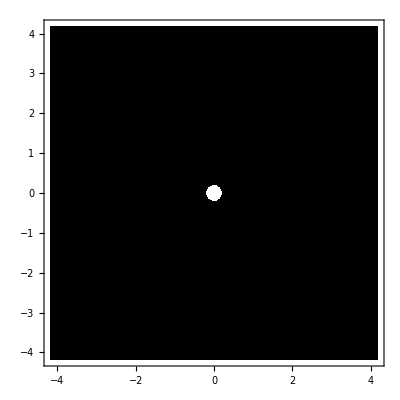

```mathematica
StreamDensityPlot[{x,y},{x, -4, 4},{y,-4,4},RegionFunction->Function[{x,y,vx,vy,n},x^2+y^2>0.05]]
```

### Example-2

Lets take a look at a 3-dimensional example:

v⃗=x î+y ĵ+z ĵ
w⃗=-y î+x ĵ+z k̂

```mathematica
VectorPlot3D[{x,y,z},{x, -4, 4},{y,-4,4},{z,-4,4},VectorScale->0.06]
```

-Graphics3D-

### Field Lines and Equipotential Surfaces

We will now explore some advanced  plotting methods through a few basic electrodynamics problems.

Electric field for a point charge q located at a point P whose position is represented by (r⃗)_q is given by

E⃗=q/(4π ϵ_0)(r⃗-(r⃗)_q)/(|r⃗-(r⃗)_q|)^3

The potential due to this point charge at any point is given by

V(r⃗)=q/(4π ϵ_0)1/(|r⃗-(r⃗)_q|)

### Example: Dipole

Consider an electric dipole made by two charges +q and -q placed at origin and (a,0). The electric field for this set-up is given by

E⃗=q/(4π ϵ_0)(r⃗)/r^3-q/(4π ϵ_0)(r⃗-a î)/(|r⃗-a î|)^3

Non-dimensionalizing the electric field, we get

(E⃗)/(q/(4π ϵ_0 a^2))=(r⃗/a)/(r/a)^3-((r⃗)/a-î)/(|(r⃗)/a-î|)^3
ℰ⃗={X/(√(X^2+Y^2))-(X-1)/(√((X-1)^2+Y^2)),Y/(√(X^2+Y^2))-Y/(√((X-1)^2+Y^2))}

where in the second line we have written the result in terms of dimensionless X=x/a and Y=y/a.

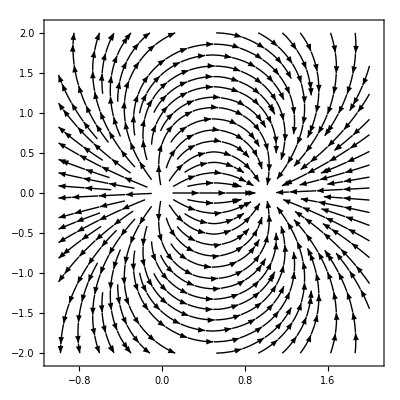

```mathematica
fieldLines=StreamPlot[{x/r^3-(x-1)/r1^3,y/r^3-y/r1^3}/.r->√(x^2+y^2)/.r1->√((x-1)^2+y^2),{x,-1,2},{y,-2,2},RegionFunction->Function[{x,y,vx,vy,n},x^2+y^2>0.01&&(x-1)^2+y^2>0.01]]
```

For potential also we will non-dimensionalize and use the ContourPlot to create contour plots

V(r)=q/(4π ϵ_0)1/r-q/(4π ϵ_0)1/(|r⃗-a î|)
V/(q/(4π ϵ_0 a))=1/(r/a)-1/(|(r⃗)/a-î|)=1/(√(X^2+Y^2))-1/(√((X-1)^2+Y^2)),

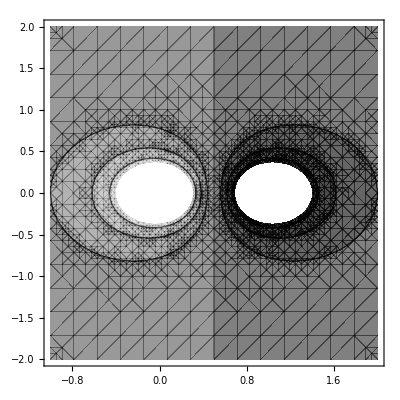

```mathematica
equiPotential=ContourPlot[{1/r-1/r1}/.r->√(x^2+y^2)/.r1->√((x-1)^2+y^2),{x,-1,2},{y,-2,2}]
```

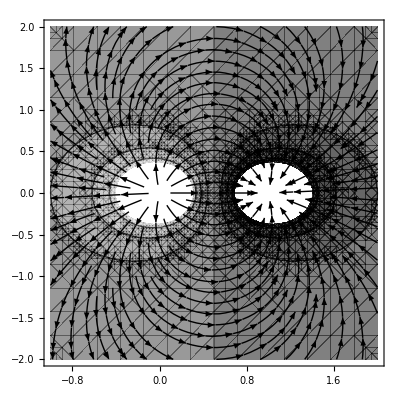

```mathematica
Show[equiPotential,fieldLines]
```

### Homework

1. Sketch the following functions, first on a piece of paper analyzing them for their zeros, divergences, extrema and asymptotes. Next cross-check your sketch by plotting the function on Mathematica.

Hyperbolic functions:

1.  cosh(x)     2.  sinh(x)     3.  tanh(x)   4.  cosech(x)    5.  sech(x)   6. coth(x).

7.  ln x           8.  ln(ln(x))    9.  ln(x)/x   10.  ln(e^x-1)   11.   ln ((1-x)/(1+x))   12.  1/x ln ((1-x)/(1+x))

13.  e^-x cos(x)     14.  e^-x sin(x)    15.  e^(-|x|)cos(x)   16.  e^(-|x|)sin(x)   17.   x e^(-x^2)   18.  x-1+e^-x

19.  x^x           20.  x^(1/x)    21.  x^(|x|)  22.  (|x|)^(|x|)  23. (|x|)^(1/2)/(1+(|x|)^(1/2))  24. (|x|)^(1/2)/(e^x+1)

25.   e^(1/x)   26.  e^(-1/x^2)  27. x^-12-x^-6   28. cosh^-1(x)  29. coth^-1(x)   30. coth(x)-1/x

2. Electric field lines of a quadrupole: Plot the electric field lines and equipotential surfaces for the quadrupolar configuration:  four charges of same magnitude and alternating sign on the corners of a square of side a, that is, +q at (0,0) and (a,a) while -q at (a,0) and (0,a). Use combination of StreamPlot and ContourPlot as shown in this lecture inside a Show function.